```mathematica
phi[n0_,n1_,n2_,n3_]:=-n0*Log[1-n3]+n1*n2/(1-n3)+n2^3*(n3+(1-n3)^2*Log[1-n3])/(36*Pi*n3^2*(1-n3)^2)
```

```mathematica
f[ϵ12_,λ1_,λ2_,q_,e1_,e2_]:= phi[3/(4*Pi)*(e1/R1^3+e2/R2^3),3/(4*Pi)*(e1/R1^2+e2/R2^2),3*(e1/R1+e2/R2),e1+e2]-e1*(λ1+λ2/q)^3*ϵ12*3*e2/(4*Pi*R2^3)/.{R2->R1/q};
```

```mathematica
eta1l = 0.31502009529;
eta1v=0.01936600948;
eps2=0.4235;
Q = 1/1;
l1 = 1.5;
l2=1+Q*(l1-1);
eta1[z_]:=eta1v+(eta1l-eta1v)/(1+Exp[-1.79*z])
```

```mathematica
veff[ϵ12_,λ1_,λ2_,q_,e1_]:=1/q^3(e1/(1-e1)-(3 e1 (-q (1+q)+e1 (-1+q+q^2)))/(-1+e1)^2-e1 ϵ12 (q λ1+λ2)^3-q^3*Log[1-e1]+(e1 (e1+2 (-1+e1) Log[1-e1]))/(-1+e1)^2+((2-3 q+e1(-4+3 q)) (e1+(-1+e1)^2 Log[1-e1]))/(-1+e1)^3)+0.18
(*veff[ϵ12_,λ1_,λ2_,q_,e1_]:=SeriesCoefficient[4*Pi/3*R2^3*f[ϵ12,λ1,λ2,q,e1,e2]/.{R2->R1/q},{e2,0,1}];*)
```

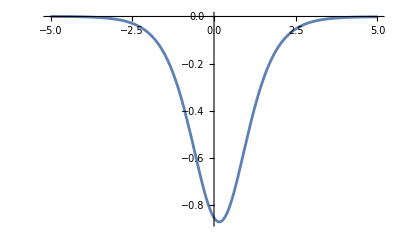

```mathematica
Plot[veff[Sqrt[1*eps2],l1,l2,Q,eta1[z]],{z,-5,5}]
```

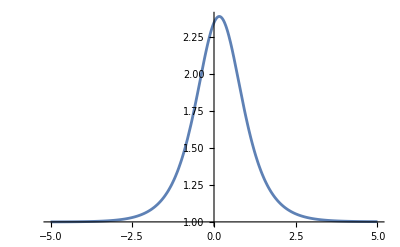

```mathematica
Plot[Exp[-veff[Sqrt[1*eps2],l1,l2,Q,eta1[z]]],{z,-5,5}]
```

```mathematica
Manipulate[Plot[veff[eps,l1,l2,Q,eta1[z]],{z,-5,5}],{eps,0,2}]
```